# Variational minimisation

This notebook analytically and numerically explores variational minimisation, demonstrating quantum gradient descent and quantum natural gradient.

Contents:
    • Analytic
    • Gradient descent
    • Natural gradient

Tyson Jones, 2024
Department of Materials, University of Oxford
tyson.jones.input@gmail.com

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

## Analytic

Variational quantum algorithms make use of a parameterised “ansatz” circuit U(θ⃗) acting upon a fixed input state in, in order to produce parameterised states ψ(θ⃗). For example, consider this three-qubit ansatz with parameters  θ⃗ = {a, b}.

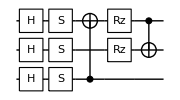

```mathematica
nQb = 3;
u = Circuit[  Subscript[H, 0] Subscript[S, 0] Subscript[H, 1] Subscript[S, 1] Subscript[H, 2] Subscript[S, 2] Subscript[C, 0][Subscript[X, 2]] Subscript[Rz, 2][a] Subscript[Rz, 1][b] Subscript[C, 2][Subscript[X, 1]]   ];
DrawCircuit[u]
```

Let’s use a fixed input state in = 0.

```mathematica
in = UnitVector[2^nQb, 1]
```

{1,0,0,0,0,0,0,0}

We can express our ansatz state ψ(θ⃗) analytically as a function of a and b

```mathematica
ψ = CalcCircuitMatrix[u] . in // Simplify
```

{ⅇ^(-1/2 ⅈ (a+b))/(2 √2),-ⅇ^(-1/2 ⅈ (a+b))/(2 √2),(ⅈ ⅇ^(-1/2 ⅈ (a-b)))/(2 √2),-(ⅈ ⅇ^(-1/2 ⅈ (a-b)))/(2 √2),-ⅇ^(1/2 ⅈ (a+b))/(2 √2),-ⅇ^(1/2 ⅈ (a+b))/(2 √2),(ⅈ ⅇ^(1/2 ⅈ (a-b)))/(2 √2),(ⅈ ⅇ^(1/2 ⅈ (a-b)))/(2 √2)}

An experimentalist could freely change the values of parameters a and b, smoothly changing the output quantum state. For instance, here’s how the fidelity with the + state would change as b is varied (incidentally, it is independent of a).

```mathematica
plus = ConstantArray[1/(√(2^nQb)),2^nQb];
fid = Simplify[ Abs[ψ . plus]^2,  {a,b} ∈Reals]
```

1/16 Abs[-ⅈ+ⅇ^(ⅈ b)]^2

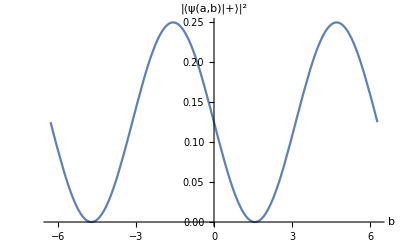

```mathematica
Plot[fid, {b,-2π,2π}, AxesLabel->{"b","|⟨ψ(a,b)|+⟩|^2"}]
```

We are often interested in the observables of some operator, like a Hamiltonian, natively expressed as a Pauli string. Here’s one I just made up:

```mathematica
h = Subscript[X, 0] Subscript[Y, 1]  + 2 Subscript[Z, 1] Subscript[Z, 2] - 3 Subscript[Y, 0] Subscript[Y, 2] ;
```

and here is now it looks as a 3-qubit Z-basis matrix:

```mathematica
hM = Normal @ CalcPauliExpressionMatrix[h];
MatrixForm[hM]
```

(2 | 0 | 0 | -ⅈ | 0 | 3 | 0 | 0
0 | 2 | -ⅈ | 0 | -3 | 0 | 0 | 0
0 | ⅈ | -2 | 0 | 0 | 0 | 0 | 3
ⅈ | 0 | 0 | -2 | 0 | 0 | -3 | 0
0 | -3 | 0 | 0 | -2 | 0 | 0 | -ⅈ
3 | 0 | 0 | 0 | 0 | -2 | -ⅈ | 0
0 | 0 | 0 | -3 | 0 | ⅈ | 2 | 0
0 | 0 | 3 | 0 | ⅈ | 0 | 0 | 2)

By studying the expectation value of this observable upon states output from our ansatz circuit, we are effectively probing a parameterised manifold of the observable space.

```mathematica
v = Conjugate[ψ] . hM . ψ;
v = FullSimplify[v,{a,b}∈Reals]
```

-Cos[b]+3 Sin[a] Sin[b]

```mathematica
Plot3D[v,{a,-2π,2π},{b,-2π,2π}, AxesLabel->{"a","b","⟨ψ|h|ψ⟩"}]
```

-Graphics3D-

Often we are interested in the minimum eigenvalue of the observable. If our operator h is a Hamiltonian, this is the ground-state energy.

```mathematica
Min @ Eigenvalues @ hM
```

-√14

Alas, our parameterised circuit generates only a strict subspace of states ψ(θ⃗), which is unlikely to contain the true ground-state. Indeed, the lowest our circuit above can produce is:

```mathematica
MinValue[v,{a,b}]
```

-√10

In principle, we can add more parameters to our circuit and increase the size of our accessible subspace. Here, we’ll add introduce additional controlled rotations with parameters c and d...

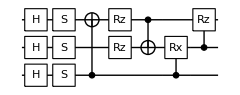

```mathematica
u = Join[u, { Subscript[C, 0][Subscript[Rx, 1][c]],  Subscript[C, 1][Subscript[Rz, 2][d]]}];
DrawCircuit[u]
```

```mathematica
ψ = CalcCircuitMatrix[u] . in;
v = Conjugate[ψ] . hM . ψ;
v = FullSimplify[v,{a,b,c,d}∈Reals]
```

1/2 Cos[c/2] (-3 Cos[a+b]-2 Cos[b-d/2]+3 Cos[a-b+d]+4 Cos[b] Sin[c/2])

which enables producing states a little closer to the groundstate at -√14≈  -3.74

```mathematica
NMinimize[v,{a,b,c,d}] // Chop
```

{-3.63226,{a→-0.321751,b→0,c→-0.855463,d→-2.49809}}

Beware that a larger parameterised observable space is slower to explore! With only a few more parameters and qubits, our variational system also would become too large to study analytically like we do here, and we would have to resort to numerical study, as we do below.

## Gradient descent

Let’s consider a random 7-qubit 30-term Hamiltonian

```mathematica
nQb = 7;
h = GetRandomPauliString[nQb, 30, {-1,1}]
```

0.8042 X_1 X_3+0.588717 X_0 X_5 X_6 Y_1-0.913716 X_2 X_3 Y_0 Y_1 Y_4 Y_6+0.954613 X_0 Y_2 Y_4 Y_5 Z_1-0.0842519 X_2 X_5 Y_0 Y_3 Y_4 Y_6 Z_1+0.740256 X_1 X_3 X_4 Y_5 Z_2-0.714507 X_3 X_4 Y_1 Y_5 Z_2+0.403638 X_6 Y_1 Y_5 Z_2+0.675392 X_5 Y_0 Y_4 Z_1 Z_2+0.485387 X_2 X_5 Y_0 Y_1 Y_6 Z_3+0.769312 X_1 X_6 Y_0 Y_2 Y_3 Z_4-0.027828 X_2 X_3 X_5 Y_1 Z_0 Z_4+0.652981 X_0 X_1 X_2 X_5 Y_6 Z_3 Z_4-0.421427 X_2 X_5 X_6 Y_1 Z_0 Z_3 Z_4+0.379304 X_0 X_4 Y_1 Y_6 Z_5+0.113742 X_1 X_2 Y_4 Z_0 Z_5-0.972824 X_3 Y_4 Y_6 Z_0 Z_5+0.0600258 X_6 Y_0 Y_1 Z_3 Z_5-0.384336 X_1 Z_0 Z_3 Z_5-0.366232 X_0 X_2 X_4 Y_6 Z_1 Z_3 Z_5-0.582251 X_0 X_1 X_2 X_6 Y_3 Z_4 Z_5-0.833795 X_3 X_5 Y_0 Y_1 Y_2 Z_6-0.705635 X_1 X_2 Y_4 Z_0 Z_3 Z_6-0.515419 X_3 X_5 Y_1 Z_0 Z_4 Z_6-0.867807 X_0 X_3 Y_5 Z_1 Z_4 Z_6-0.847075 X_0 Y_1 Y_2 Z_3 Z_4 Z_6+0.25922 X_0 X_1 Y_3 Z_5 Z_6-0.928031 Y_0 Y_3 Y_4 Z_5 Z_6-0.250159 Y_3 Z_1 Z_2 Z_5 Z_6-0.269194 X_1 X_2 X_3 Z_0 Z_4 Z_5 Z_6

```mathematica
vMin = CalcPauliStringMinEigVal[h]
```

-6.45173

Imagine a quantum experimentalist seeks the ground-state energy of this Hamiltonian, and can freely vary 56 parameterised gates in their ansatz circuit u(θ⃗) which is applied to initial state +.

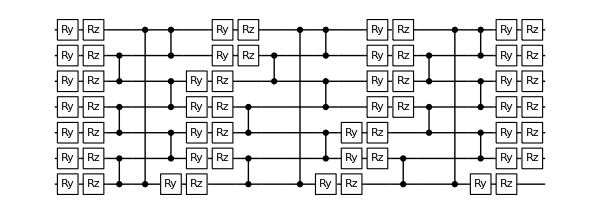

```mathematica
u = GetKnownCircuit["HardwareEfficientAnsatz", 3, θ, nQb];
DrawCircuit[u]
```

```mathematica
nθ = Max @ Cases[u, θ[i_]:>i, ∞]
```

56

We will numerically simulate the experimental process, so we prepare some quantum registers in our simulator.

```mathematica
{ψ, ϕ,in} = CreateQuregs[nQb, 3];
InitPlusState[in];
```

The experimentalist cannot study an analytic expression of their ansatz state ψ(θ⃗)=u(θ⃗)+, nor its expectation value, which are exponentially expensive! Instead, they can only measure the observable ⟨E(θ⃗)⟩ = ψ(θ⃗)hψ(θ⃗) at specific values of θ⃗.

```mathematica
CloneQureg[ψ, in];
```

```mathematica
u /. θ[_] :> RandomReal[]
```

{Ry_0[0.379964],Rz_0[0.416136],Ry_1[0.516909],Rz_1[0.745819],Ry_2[0.253023],Rz_2[0.782511],Ry_3[0.483642],Rz_3[0.358359],Ry_4[0.987236],Rz_4[0.0847689],Ry_5[0.233927],Rz_5[0.606911],Ry_6[0.804772],Rz_6[0.900195],C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_0],C_1[Z_2],C_3[Z_4],C_5[Z_6],Ry_0[0.178302],Rz_0[0.764123],Ry_1[0.633428],Rz_1[0.176239],Ry_2[0.825577],Rz_2[0.0903814],Ry_3[0.0710499],Rz_3[0.325454],Ry_4[0.114324],Rz_4[0.71113],Ry_5[0.408383],Rz_5[0.872261],Ry_6[0.0330232],Rz_6[0.172492],C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_0],C_1[Z_2],C_3[Z_4],C_5[Z_6],Ry_0[0.519215],Rz_0[0.899798],Ry_1[0.782472],Rz_1[0.0897789],Ry_2[0.0161363],Rz_2[0.757917],Ry_3[0.979974],Rz_3[0.195149],Ry_4[0.276458],Rz_4[0.448323],Ry_5[0.955637],Rz_5[0.427049],Ry_6[0.239681],Rz_6[0.150582],C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_0],C_1[Z_2],C_3[Z_4],C_5[Z_6],Ry_0[0.267701],Rz_0[0.17584],Ry_1[0.0386318],Rz_1[0.196578],Ry_2[0.72915],Rz_2[0.375773],Ry_3[0.275606],Rz_3[0.513447],Ry_4[0.6292],Rz_4[0.747971],Ry_5[0.0212156],Rz_5[0.836306],Ry_6[0.0610466],Rz_6[0.549128]}

```mathematica
ApplyCircuit[ψ, %];
CalcExpecPauliString[ψ, h, ϕ]
```

-0.0822767

The parameter space is already too big to randomly sample like this. We are very unlikely to randomly choose parameters near the ground-state, especially given the barren plateaus.

```mathematica
samples = Table[
	CloneQureg[ψ, in];
	ApplyCircuit[ψ, u /.θ[_] :> RandomReal[] ];
	CalcExpecPauliString[ψ, h, ϕ],
	20
]
```

{0.290054,0.0354827,0.54823,0.242395,0.0316951,0.403997,0.241329,0.573669,0.261465,0.371843,0.241047,0.100007,0.124764,0.381409,-0.168843,0.565205,0.418175,-0.1838,0.287822,0.337146}

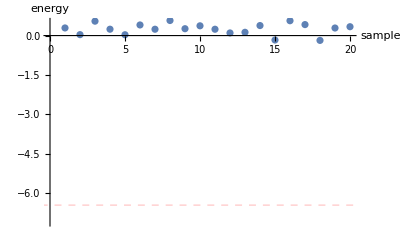

```mathematica
ListPlot[samples, PlotRange->{1.1vMin,.5}, GridLines->{{},{{vMin,Directive[Red,Dashed]}}}, AxesLabel->{"sample","energy"}]
```

The experimentalist could instead employ quantum gradient descent, treating the observable’s expectation value as the cost function to be minimised. This requires they can additionally obtain the gradient of the observable,  ∇_(θ⃗) ψ(θ⃗)hψ(θ⃗), at a given position in parameter space. One method to do so is via the parameter shift rule.

Consider a unitary gate of form U(θ) = exp(-ⅈ a θ G) with Hermitian generator G, and observable  ⟨E(θ)⟩ = ψU^†(θ) H U(θ)ψ. The parameter shift rule states that d/dθ⟨E(θ)⟩ = r [ ⟨E(θ+π/(4r))⟩ - ⟨E(θ-π/(4r))⟩ ]  where r = a/2(e_1-e_0) , and e_0 and e_1 are the eigenvalues of G. Assuming all ansatz gates depend on unique parameters, this expression gives the full circuit’s derivative.

Because we our ansatz is composed of Ry = exp(-ⅈ θ/2 Y) and Rz = exp(-ⅈ θ/2 Z), which have Y and Z generators with ±1 eigenvalues, we know that a=1/2 and r=a, so that d/dθ⟨E(θ)⟩ = 1/2 [ ⟨E(θ+π/2)⟩ - ⟨E(θ-π/2)⟩ ] . Our experimentalist only needs to obtain two expectation values in order to find the derivative of the expectation with respect to a parameter. They don’t need any new circuits - they just sample the ansatz circuit!

```mathematica
calcExpecDeriv[h_, in_, u_, vθ_, dθ_, ψ_, ϕ_] := Module[
	{v1,v2,e1,e2},

	v1 = vθ  /. (dθ->v_) :> (dθ->v+π/2);
	v2 = vθ  /. (dθ->v_) :> (dθ->v-π/2);

	CloneQureg[ψ, in];
	ApplyCircuit[ψ, u /.v1];
	e1 = CalcExpecPauliString[ψ, h, ϕ];

	CloneQureg[ψ, in];
	ApplyCircuit[ψ, u /.v2];
	e2 = CalcExpecPauliString[ψ, h, ϕ];

	(e1-e2)/2
]
```

Let’s randomly initialise our parameters to values vθ, and check the corresponding energy.

```mathematica
vθ = Table[θ[i]->RandomReal[], {i,nθ}]
initθ = vθ;
```

{θ[1]→0.944783,θ[2]→0.674455,θ[3]→0.0508029,θ[4]→0.381874,θ[5]→0.947617,θ[6]→0.803537,θ[7]→0.518898,θ[8]→0.12349,θ[9]→0.00541244,θ[10]→0.633603,θ[11]→0.708769,θ[12]→0.330352,θ[13]→0.84117,θ[14]→0.300132,θ[15]→0.315277,θ[16]→0.38555,θ[17]→0.807733,θ[18]→0.493529,θ[19]→0.235609,θ[20]→0.499855,θ[21]→0.984375,θ[22]→0.912659,θ[23]→0.273329,θ[24]→0.353283,θ[25]→0.399153,θ[26]→0.549364,θ[27]→0.983178,θ[28]→0.889903,θ[29]→0.0928538,θ[30]→0.975794,θ[31]→0.807838,θ[32]→0.16291,θ[33]→0.802887,θ[34]→0.842839,θ[35]→0.415662,θ[36]→0.647286,θ[37]→0.494067,θ[38]→0.349075,θ[39]→0.880707,θ[40]→0.620367,θ[41]→0.453247,θ[42]→0.000729754,θ[43]→0.564278,θ[44]→0.919765,θ[45]→0.607461,θ[46]→0.248741,θ[47]→0.784312,θ[48]→0.838105,θ[49]→0.0971372,θ[50]→0.889634,θ[51]→0.152776,θ[52]→0.461625,θ[53]→0.957948,θ[54]→0.375586,θ[55]→0.786615,θ[56]→0.0641479}

```mathematica
CloneQureg[ψ, in];
ApplyCircuit[ψ, u /.vθ];
CalcExpecPauliString[ψ, h, ϕ]
```

0.358099

Here are the derivatives d/dθ[1]⟨E(θ)⟩ and d/dθ[2]⟨E(θ)⟩

```mathematica
calcExpecDeriv[h, in, u, vθ, θ[1], ψ, ϕ]
```

0.120587

```mathematica
calcExpecDeriv[h, in, u, vθ, θ[2], ψ, ϕ]
```

-0.0609789

Obtaining the gradient at parameter values vθ therefore requires evaluating 2 nθ  expectation values.

```mathematica
grad = Table[
	calcExpecDeriv[h, in, u, vθ, θ[i], ψ, ϕ],
	{i, nθ}
]
```

{0.120587,-0.0609789,-0.0617724,-0.316569,-0.0206436,-0.234134,-0.175736,0.25312,0.330288,-0.156502,-0.129305,-0.103314,-0.189972,0.0314764,0.152959,-0.0179045,0.279813,-0.352306,-0.0275923,-0.22221,0.203336,-0.021528,0.309561,-0.060743,0.139741,-0.154059,0.234719,-0.266365,0.076402,-0.00489835,-0.205105,-0.146627,-0.391673,-0.0854651,0.103386,-0.160257,0.383993,0.016442,0.123013,-0.143761,0.0446333,-0.383324,-0.119879,0.212571,0.503745,-0.134012,-0.0179596,-0.16494,0.32401,-0.164754,0.00892003,0.0577206,0.178624,-0.0516252,0.136484,-0.399077}

Gradient descent simply instructs the experimentalist to update the parameters in the opposite direction to this gradient, in order to reduce the cost function. That is:
        Δ θ⃗ = - ∇⟨E(θ⃗)⟩

```mathematica
Δt = 0.1;
vθ[[All,2]] -= Δt grad;
```

```mathematica
CloneQureg[ψ, in];
ApplyCircuit[ψ, u /.vθ];
CalcExpecPauliString[ψ, h, ϕ]
```

0.120877

Indeed the expectation value has reduced! This process can be repeated, iteratively minimising the cost function.

```mathematica
vθ = initθ;
gradVals = Table[
	grad = Table[calcExpecDeriv[h, in, u, vθ, θ[i], ψ, ϕ],{i, nθ}];
	vθ[[All,2]] -= Δt grad;

	ApplyCircuit[CloneQureg[ψ, in], u /.vθ];
	CalcExpecPauliString[ψ, h, ϕ],
	30
];
```

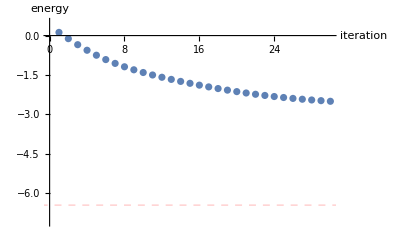

```mathematica
ListPlot[gradVals, 
	AxesLabel->{"iteration", "energy"}, 
	PlotRange->{1.1vMin,.5}, 
	GridLines->{{},{{vMin,Directive[Red,Dashed]}}}]
```

We have effectively simulated quantum natural gradient in a noise-free setting. Let’s now introduce decoherence into our ansatz circuit, inserting dephasing noise after every Rz, and two-qubit depolarising noise after every control-Z.

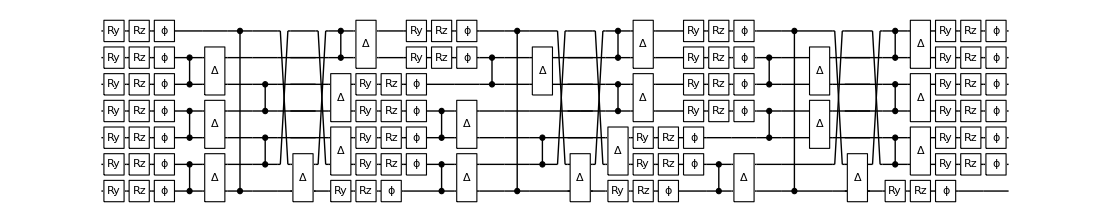

```mathematica
ch = u /. {
	g:Subscript[Rz, t_][_]:>Sequence[g,Subscript[Deph, t][10^-3]],
	g:Subscript[C, c_][Subscript[Z, t_]] :> Sequence[g, Subscript[Depol, c,t][10^-2]]};

DrawCircuit[ch]
```

By now merely changing our states to be density matrices...

```mathematica
{ρ, μ,in} = CreateDensityQuregs[nQb, 3];
InitPlusState[in];
```

all our previous calculations can be repeated in the presence of noise.

```mathematica
CloneQureg[ρ, in];
ApplyCircuit[ρ, ch /.vθ];
CalcExpecPauliString[ρ, h, μ]
```

-1.9876

We can see that the introduced decoherence has damaged the fidelity of the final state.

```mathematica
CalcPurity[ρ]
```

0.652987

```mathematica
CalcFidelity[ρ,ψ]
```

0.807163

Let’s see how the full evolution of gradient descent would differ if noise were present at every iteration.

```mathematica
vθ = initθ;
noisyGradVals = Table[
	grad = Table[calcExpecDeriv[h, in, ch, vθ, θ[i], ρ, μ],{i, nθ}];
	vθ[[All,2]] -= Δt grad;

	ApplyCircuit[CloneQureg[ρ, in], ch /.vθ];
	CalcExpecPauliString[ρ, h, μ],
	30
];
```

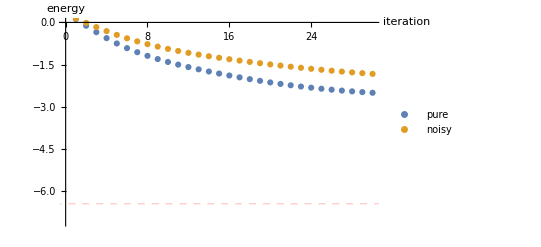

```mathematica
ListPlot[{gradVals,noisyGradVals}, 
	AxesLabel->{"iteration", "energy"}, 
	PlotLegends->{"pure", "noisy"},
	PlotRange->{0,1.1vMin},
	GridLines->{{},{{vMin,Directive[Red,Dashed]}}}]
```

## Natural gradient

Superior quantum minimisation techniques exist which converge faster than gradient descent, and more reliably, while requiring only a modest increase in experimental measurements. One such technique is natural gradient which prescribes a change in parameters Δ θ⃗ given by:
        Re[G]  (Δ θ⃗) = - Δt  ∇⟨E(θ⃗)⟩
        
The matrix Re[G] is the Fubini-Study metric tensor, equivalent to the real component of the quantum geometric tensor with entries:
        G_ij = (∂ψ(θ⃗))/(∂θ_i)(∂ψ(θ⃗))/(∂θ_j) -((∂ψ(θ⃗))/(∂θ_i)ψ(θ⃗) )  ( ψ(θ⃗)(∂ψ(θ⃗))/(∂θ_j)) 
        
This horrifying looking matrix is thankfully straightforward to evaluate on a quantum computer. And because we have the luxury of simulating the algorithm, rather than executing its prescribed circuits on experimental hardware, we can even just directly evaluate the matrix G using:

```mathematica
?CalcMetricTensor
```

Let’s return to pure-state simulation, and re-randomise the ansatz parameters

```mathematica
{ψ, ϕ,in} = CreateQuregs[nQb, 3];
InitPlusState[in];
```

```mathematica
vθ = Table[θ[i]->RandomReal[], {i,nθ}]
```

{θ[1]→0.0824625,θ[2]→0.31652,θ[3]→0.459314,θ[4]→0.807564,θ[5]→0.237396,θ[6]→0.528357,θ[7]→0.815375,θ[8]→0.750482,θ[9]→0.830971,θ[10]→0.698174,θ[11]→0.740431,θ[12]→0.0252106,θ[13]→0.594864,θ[14]→0.154642,θ[15]→0.16513,θ[16]→0.240785,θ[17]→0.95795,θ[18]→0.119302,θ[19]→0.97886,θ[20]→0.562465,θ[21]→0.314392,θ[22]→0.224505,θ[23]→0.322188,θ[24]→0.401244,θ[25]→0.288787,θ[26]→0.137886,θ[27]→0.805133,θ[28]→0.338753,θ[29]→0.520798,θ[30]→0.543042,θ[31]→0.442366,θ[32]→0.947235,θ[33]→0.407512,θ[34]→0.484981,θ[35]→0.309018,θ[36]→0.124111,θ[37]→0.620958,θ[38]→0.945303,θ[39]→0.816339,θ[40]→0.455867,θ[41]→0.280547,θ[42]→0.381771,θ[43]→0.418341,θ[44]→0.498481,θ[45]→0.900826,θ[46]→0.652939,θ[47]→0.934518,θ[48]→0.225505,θ[49]→0.133524,θ[50]→0.742551,θ[51]→0.290751,θ[52]→0.969005,θ[53]→0.530504,θ[54]→0.781994,θ[55]→0.568455,θ[56]→0.276424}

The Fubini-Study metric tensor is trivially obtained:

```mathematica
g = Re @ CalcMetricTensor[in, u, vθ];
g[[50;;, 50;;]] // Chop // MatrixForm
```

(0.249999 | 0.0006693 | 0.0103687 | -0.0153045 | 0.00411197 | 0.00853124 | 0.0111326
0.0006693 | 0.249838 | 0.000244921 | 0.00291078 | 0.00240679 | 0.0347412 | 0.0133983
0.0103687 | 0.000244921 | 0.24963 | 0.00762959 | 0.00303132 | -0.0167092 | -0.00565139
-0.0153045 | 0.00291078 | 0.00762959 | 0.247566 | -0.00219198 | -0.0134712 | 0.00640067
0.00411197 | 0.00240679 | 0.00303132 | -0.00219198 | 0.248026 | -0.0124202 | 0.0142553
0.00853124 | 0.0347412 | -0.0167092 | -0.0134712 | -0.0124202 | 0.25 | 1.29301×10^-7
0.0111326 | 0.0133983 | -0.00565139 | 0.00640067 | 0.0142553 | 1.29301×10^-7 | 0.249922)

The energy gradient, also required by quantum natural gradient, can be obtained in an identical manner to that of quantum gradient descent - via the parameter-shift rule. However, it is more convenient make use of another function below, which uses back-propagation to run O(#gates) faster!

```mathematica
?CalcExpecPauliStringDerivs
```

```mathematica
grad = CalcExpecPauliStringDerivs[in, u, vθ, h]
```

{0.24538,0.106511,0.122928,0.119399,-0.0220159,0.128087,-0.0589124,0.356504,0.0371179,-0.20374,0.350681,0.0476721,0.0982792,-0.108923,0.248425,0.10902,-0.219147,-0.0520782,-0.134164,-0.00339067,0.313054,0.36457,-0.0214842,-0.0897153,0.375175,0.00480845,0.35326,-0.0401864,-0.143416,-0.0361575,-0.0823219,-0.114158,-0.151913,0.012574,-0.155273,0.391916,-0.240681,-0.00291144,0.183757,-0.00738578,0.0687664,-0.00819604,0.140992,0.00546608,0.193064,-0.346827,0.0245652,0.0320816,0.621942,0.339881,-0.148997,-0.0181471,0.409203,0.0321777,0.276417,0.157329}

Now that we have obtained Re[G] and ∇⟨E(θ⃗)⟩,  computing an iteration of natural gradient requires solving the below linear equation for the change in parameters, Δ θ⃗.
        Re[G]  (Δ θ⃗) = - Δt   ∇⟨E(θ⃗)⟩
        
Alas we cannot simply invert G to obtain  Δ θ⃗ = - Δt   Re[G]^-1   ∇⟨E(θ⃗)⟩, because it is often singular!

```mathematica
Det[g]
```

2.919×10^-72

Instead, we seek an approximate solution - there are many ways to do this!

```mathematica
Δθ = LinearSolve[g, -Δt grad]
```

{-0.465391,0.664162,-0.528219,-0.492678,-0.0402829,-0.576641,-0.133898,-0.628493,0.671918,0.799776,-0.455777,0.0848771,0.476907,-0.0898445,-0.262464,-1.23912,-0.134213,-0.754336,-0.729321,0.52531,0.445998,0.0802577,-0.114921,0.602765,0.445231,-0.212191,-0.285996,1.66092,0.435719,-0.355767,0.614801,0.780978,0.353793,-0.547958,0.157621,-1.24833,-0.733746,-0.87831,0.182781,0.705881,-0.251065,-2.17302,0.0563383,0.93814,0.150695,0.331929,0.482414,0.948237,-0.581249,1.00339,-0.0569486,0.209921,-0.438878,-0.367177,0.119752,0.582094}

```mathematica
Δθ = -Δt  PseudoInverse[g] . grad
```

{-0.465391,0.664162,-0.528219,-0.492678,-0.0402829,-0.576641,-0.133898,-0.628493,0.671918,0.799776,-0.455777,0.0848771,0.476907,-0.0898445,-0.262464,-1.23912,-0.134213,-0.754336,-0.729321,0.52531,0.445998,0.0802577,-0.114921,0.602765,0.445231,-0.212191,-0.285996,1.66092,0.435719,-0.355767,0.614801,0.780978,0.353793,-0.547958,0.157621,-1.24833,-0.733746,-0.87831,0.182781,0.705881,-0.251065,-2.17302,0.0563383,0.93814,0.150695,0.331929,0.482414,0.948237,-0.581249,1.00339,-0.0569486,0.209921,-0.438878,-0.367177,0.119752,0.582094}

```mathematica
Δθ = Fit[{g, -Δt grad}, FitRegularization->{"Tikhonov", 10^-10}]
```

{-0.465406,0.663854,-0.528191,-0.492677,-0.0403096,-0.576662,-0.133886,-0.628557,0.671896,0.799712,-0.45575,0.0848979,0.476797,-0.0898166,-0.262497,-1.23876,-0.134266,-0.75432,-0.729284,0.525333,0.445972,0.0803299,-0.114905,0.602803,0.445198,-0.212215,-0.285993,1.66045,0.435746,-0.355744,0.61476,0.780884,0.353805,-0.547964,0.157614,-1.24801,-0.733727,-0.878255,0.182781,0.70579,-0.250976,-2.17244,0.0564028,0.938096,0.150723,0.332029,0.482384,0.948194,-0.581248,1.0031,-0.0569467,0.209875,-0.438842,-0.367145,0.119762,0.582013}

The last method is Tikhonov regularisation with parameter λ=10^-10, which obtains ((min_(θ⃗) |Re[G]  (Δ θ⃗) + Δt   ∇⟨E(θ⃗)⟩|)^2  + λ |Δ θ⃗|)^2  , additionally constraining the linear equation to minimise the size of the parameter change, enforcing smoothness.

Let’s now simulate quantum natural gradient upon the same system we threw at gradient descent.

```mathematica
vθ = initθ;
natGradVals = Table[
	grad = CalcExpecPauliStringDerivs[in, u, vθ, h];
	g = Re @ CalcMetricTensor[in, u, vθ];
	Δθ = Fit[{g, -Δt grad}, FitRegularization->{"Tikhonov", 10^-6}];
	vθ[[All,2]] += Δθ;

	ApplyCircuit[CloneQureg[ψ, in], u /.vθ];
	CalcExpecPauliString[ψ, h, ϕ],
	30
];
```

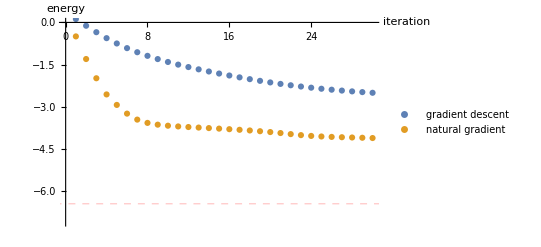

```mathematica
ListPlot[{gradVals, natGradVals},
	AxesLabel->{"iteration", "energy"},
	PlotLegends->{"gradient descent", "natural gradient"} ,
	PlotRange->{0,1.1vMin},
	GridLines->{{},{{vMin,Directive[Red,Dashed]}}}]
```

These functions are also compatible with density matrices and parameterised channels!

```mathematica
{ρ, μ,in} = CreateDensityQuregs[nQb, 3];
InitPlusState[in];
```

```mathematica
vθ = initθ;
noisyNatGradVals = Table[
	grad = CalcExpecPauliStringDerivs[in, ch, vθ, h];
	g = Re @ CalcMetricTensor[in, ch, vθ];
	Δθ = Fit[{g, -Δt grad}, FitRegularization->{"Tikhonov", 10^-6}];
	vθ[[All,2]] += Δθ;

	ApplyCircuit[CloneQureg[ρ, in], ch /.vθ];
	CalcExpecPauliString[ρ, h, μ],
	30
];
```

Let’s compare all our simulations.

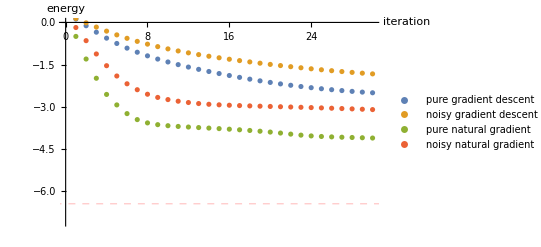

```mathematica
ListPlot[{gradVals, noisyGradVals, natGradVals, noisyNatGradVals},
	AxesLabel->{"iteration", "energy"},
	PlotLegends->{
		"pure gradient descent",
		"noisy gradient descent",
		"pure natural gradient",
		"noisy natural gradient"} ,
	PlotRange->{0,1.1vMin},
	GridLines->{{},{{vMin,Directive[Red,Dashed]}}}]
```

Note this is not an interpretable performance comparison of these methods; we have not individually optimised the timesteps Δt, nor compared their resource costs. We have made no effort to sensibly initialise our parameters, avoid barren plateaus, nor reason about convergence.

We finally mention that watching the parameters smoothly evolve during minimisation can be quite a show!

```mathematica
in = InitPlusState @ CreateQureg[nQb];
vθ = Table[θ[i]->RandomReal[], {i,nθ}];
θt = Transpose @ Table[
	grad = CalcExpecPauliStringDerivs[in, u, vθ, h];
	g = Re @ CalcMetricTensor[in, u, vθ];
	Δθ = Fit[{g, -Δt grad}, FitRegularization->{"Tikhonov", 10^-6}];
	vθ[[All,2]] += Δθ,
	30
];
```

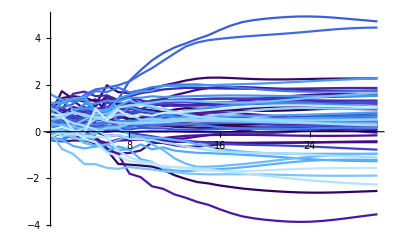

```mathematica
ListLinePlot[θt, PlotRange->{{1,All},All}, PlotStyle->"DeepSeaColors"]
```